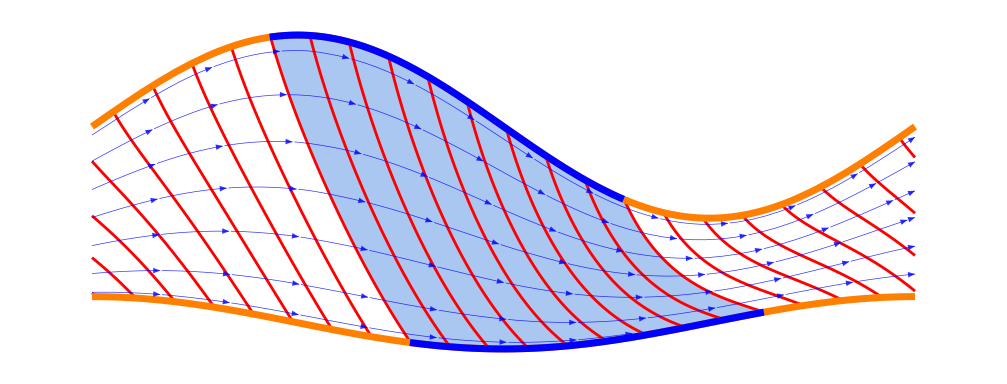

```mathematica
(* Channel construction *)
div[U_]:=D[U[[1]],x]+D[U[[2]],y];
grad[f_]:={D[f,x],D[f,y]};
createChannel[y1_,y2_]:=Module[{p,U},
p = {u,ym+w v};
p={u,y1+v(y2-y1)};
U=Simplify[D[p,u]/.v->((y-y1)/(y2-y1))/.u->x];
{p,U}
];
y1=.2Cos[u]-.5;
y2=1+.7 Sin[u];
{p,U}=createChannel[y1,y2];
ch=ParametricRegion[p,{{u,0,2Pi},{v,0,1}}];
sbs={u->(t-Pi/2)^2/2+uVal,v->t};
ch2=ParametricRegion[p/.sbs,{{uVal,.38Pi,1.24Pi},{t,0,1}}];
sw1G=ParametricPlot[p/.sbs/.t->1,{uVal,.38Pi,1.24Pi},PlotStyle->Directive[Blue,Thickness[.005],Opacity[1]]];
sw2G=ParametricPlot[p/.sbs/.t->0,{uVal,.38Pi,1.24Pi},PlotStyle->Directive[Blue,Thickness[.005],Opacity[1]]];
chG=Region[ch];
ch2G=Region[ch2];
γs=Table[p/.sbs,{uVal,-15,15,.3}];

sG=ParametricPlot[γs,{t,0,1},PlotStyle->Directive[Red,Thickness[.002],Opacity[1]],RegionFunction->Function[{x,y},0<x<2Pi]];
wG=Plot[{y1,y2},{u,0,2Pi},PlotStyle->Directive[Orange,Thickness[.005],Opacity[1]]];
UG=StreamPlot[U,{x,0,2Pi},{y,-1.5,2.8},StreamStyle->Directive[Blue,Thickness[.0005],Opacity[.8]],
RegionFunction->Function[{u,y},y1<y<y2]];
Show[ch2G,sG,UG,wG,sw1G,sw2G]
```

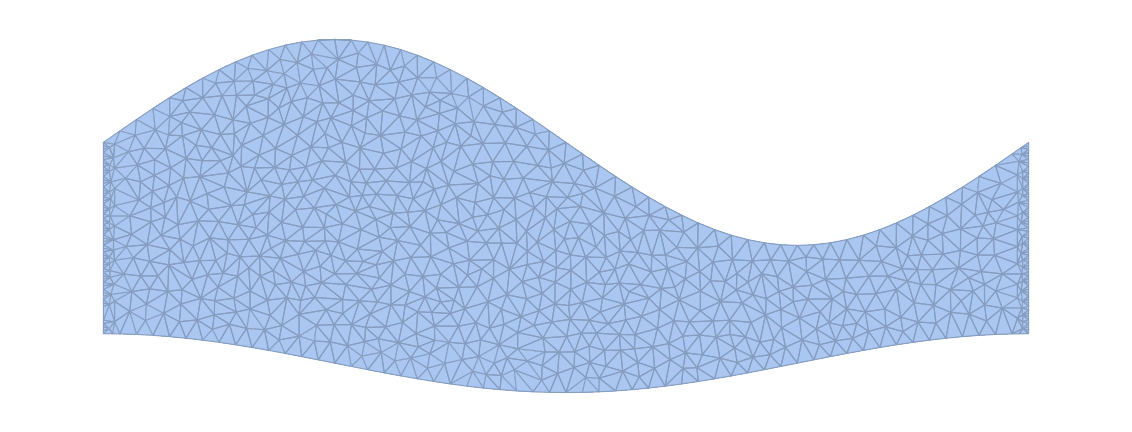

NDSolveValue::femimq: The element mesh has insufficient quality of -9244.02. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

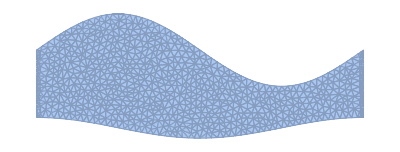
NDSolveValue[{-ϕ^(0,2)[x,y]-ϕ^(2,0)[x,y]==0,DirichletCondition[ϕ[x,y]==0.,x==0],DirichletCondition[ϕ[x,y]==1.,x==2 π]},ϕ,{x,y}∈-Graphics-]

```mathematica
rD=DiscretizeRegion[ch,MaxCellMeasure->.01,MeshQualityGoal->0]
sol=NDSolveValue[{-∇_{x,y}^2 ϕ[x,y] ==0,
DirichletCondition[ϕ[x, y] == 0.0, x==0],
DirichletCondition[ϕ[x, y] == 1.0, x==2Pi]}, ϕ, {x, y} ∈ rD];
sol
```